```mathematica
Quit
```

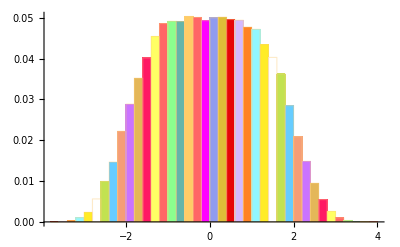

MixtureDistribution[{0.603297,0.396703},{NormalDistribution[-0.792267,0.98585],NormalDistribution[1.33602,0.748056]}]

```mathematica
data=Inner[Times,RandomChoice[{0.5,0.5}->{-1,1},{100000,100}],1./Range[100]];
Histogram[data,40,"Probability",ChartStyle->60]
FindDistribution[data,TargetFunctions->{NormalDistribution}]
```

```mathematica
随机向量
```

```mathematica
PDF[BernoulliDistribution[1/2],k]
```

Piecewise[{{1/2, k==0||k==1}, {0, True}}]

```mathematica
xd=ProbabilityDistribution[,{k,-Infinity,Infinity}]
yd=ProbabilityDistribution[Piecewise[{{s2/2,k==-1||k==1}},0],{k,-Infinity,Infinity}]
```

ProbabilityDistribution[Piecewise[{{s1/2, x==-1||x==1}, {0, True}}],{x,-∞,∞}]

ProbabilityDistribution[Piecewise[{{s2/2, x==-1||x==1}, {0, True}}],{x,-∞,∞}]

```mathematica
TransformedDistribution[x+y,{x\[Distributed]xd,y\[Distributed]yd}]
```

TransformedDistribution[x+y,{x\[Distributed]ProbabilityDistribution[Piecewise[{{s1/2, x==-1||x==1}, {0, True}}],{x,-∞,∞}],y\[Distributed]ProbabilityDistribution[Piecewise[{{s2/2, x==-1||x==1}, {0, True}}],{x,-∞,∞}]}]

```mathematica
CharacteristicFunction[BernoulliDistribution[1/2],x]
```

1/2+ⅇ^(ⅈ x)/2

```mathematica
FourierSequenceTransform[Piecewise[{{s1/2,k==-1||k==1}},0],k,t,FourierParameters->{1,1},Assumptions->s1>0]
```

1/2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t)) s1

```mathematica
FullSimplify[1/2 ⅇ^(-ⅈ t) (1+ⅇ^(2 ⅈ t)) s1]
```

s1 Cos[t]

```mathematica
BinomialDistribution
```

```mathematica
PDF[BinomialDistribution[3,1/2],k]//PiecewiseExpand
Table[%,{k,1,20}]
```

Piecewise[{{1/8 Binomial[3,k], 0≤k≤3}, {0, True}}]

{3/8,3/8,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Piecewise[{{x/8, k==-3||k==3}, {(3 x)/8, k==-1||k==1}, {0, True}}]

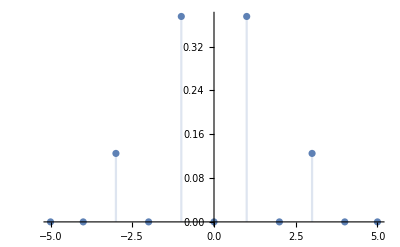

Piecewise[{{1/8, -k==-2||-k==2}, {1/4, -k==0}, {0, True}}]

```mathematica
InverseFourierSequenceTransform[x Cos[t]^3,t,-k]//PiecewiseExpand
DiscretePlot[%/.x->1,{k,-5,5}]
```

```mathematica
Product[1/i^2,{i,1,n}]Cos[t]^n
```

Cos[t]^n/(n!)^2

```mathematica
IFST[n_]:=InverseFourierSequenceTransform[Times@@Array[Subscript[s,#]&,n]Cos[t]^n,t,-k,FourierParameters->{1,1}]
```

```mathematica
Array[IFST,5]
```

{Piecewise[{{s_1/2, -k==-1||-k==1}, {0, True}}],Piecewise[{{(s_1 s_2)/4, -k==-2||-k==2}, {(s_1 s_2)/2, -k==0}, {0, True}}],Piecewise[{{1/8 s_1 s_2 s_3, -k==-3||-k==3}, {3/8 s_1 s_2 s_3, -k==-1||-k==1}, {0, True}}],Piecewise[{{1/16 s_1 s_2 s_3 s_4, -k==-4||-k==4}, {1/4 s_1 s_2 s_3 s_4, -k==-2||-k==2}, {3/8 s_1 s_2 s_3 s_4, -k==0}, {0, True}}],Piecewise[{{1/32 s_1 s_2 s_3 s_4 s_5, -k==-5||-k==5}, {5/32 s_1 s_2 s_3 s_4 s_5, -k==-3||-k==3}, {5/16 s_1 s_2 s_3 s_4 s_5, -k==-1||-k==1}, {0, True}}]}

```mathematica
InverseFourierSequenceTransform[x Cos[t]^2,t,-k,GenerateConditions->True]
```

Piecewise[{{x/4, -k==-2||-k==2}, {x/2, -k==0}, {0, True}}]

```mathematica
Integrate[
```

1/(8 z^(11/6))+1/(8 z^(7/6))+1/(8 z^(5/6))+1/(8 z^(1/6))+z^(1/6)/8+z^(5/6)/8+z^(7/6)/8+z^(11/6)/8+O[z]^(605/6)

```mathematica
Array[{#->FullSimplify@Product[z^(1/i)/2+z^(-1/i)/2,{i,1,#}]}&,6]//TableForm
```

1→(1+z^2)/(2 z)
2→((1+z) (1+z^2))/(4 z^(3/2))
3→((1+z^(2/3))^2 (1+z) (1-z^(2/3)+z^(4/3)))/(8 z^(11/6))
4→((1+√z) (1+z^(2/3))^2 (1+z) (1-z^(2/3)+z^(4/3)))/(16 z^(25/12))
5→((1+z^(2/5)) (1+√z) (1+z^(2/3)) (1+z) (1+z^2))/(32 z^(137/60))
6→((1+z^(1/3)) (1+z^(2/5)) (1+√z) (1+z^(2/3)) (1+z) (1+z^2))/(64 z^(49/20))

```mathematica
cf=CharacteristicFunction[UniformDistribution[{-1/n,1/n}],t]
cff=Product[cf//FullSimplify,{n,1,3}]
InverseFourierTransform[cff,t,x]
```

-(ⅈ (-ⅇ^(-(ⅈ t)/n)+ⅇ^((ⅈ t)/n)) n)/(2 t)

(6 Sin[t/3] Sin[t/2] Sin[t])/t^3

3/8 √(π/2) (-(-11/6+x)^2 Sign[-11/6+x]+(-7/6+x)^2 Sign[-7/6+x]+(-5/6+x)^2 Sign[-5/6+x]-(-1/6+x)^2 Sign[-1/6+x]+(1/6+x)^2 Sign[1/6+x]-(5/6+x)^2 Sign[5/6+x]-(7/6+x)^2 Sign[7/6+x]+(11/6+x)^2 Sign[11/6+x])

```mathematica
Moment[NormalDistribution[μ,σ],2]
```

```mathematica
UniformDistribution
```

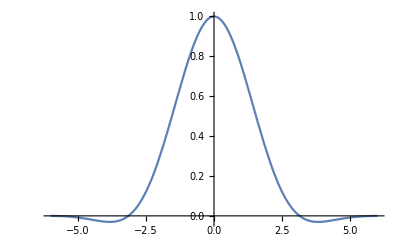

```mathematica
raw=Quiet[Table[{t,NProduct[n/t Sin[t/n],{n,1,Infinity}]},{t,-6,6,0.1}]/.{NProduct[n/t Sin[t/n],{n,1,∞}]->1}];
Plot[Evaluate@Interpolation[raw,t],{t,-6.,6.}]
```

```mathematica
fts=FullSimplify[FourierTransform[Sinc[x]Exp[-x^2/k],x,t],k>0]
```

1/2 √(π/2) (-Erf[1/2 √k (-1+t)]+Erf[1/2 √k (1+t)])

1/2 √(π/2) (-Erf[1/2 √5 (-1+x)]+Erf[1/2 √5 (1+x)])

$Aborted

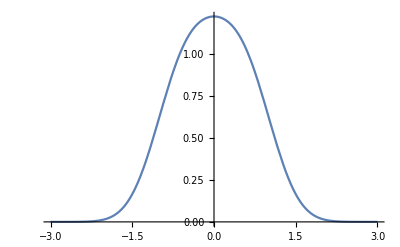

```mathematica
fts/.{t->x,k->5}
FourierTransform[%,x,t]
```

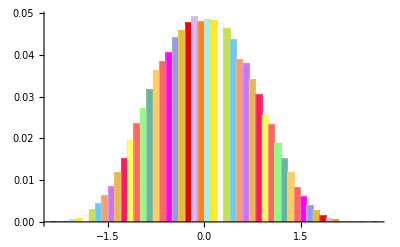

```mathematica
exp[k_]:=(1/2)*Sqrt[Pi/2]*(Erf[(1/2)*Sqrt[k]*(1 + t)]-Erf[(1/2)*Sqrt[k]*(-1 + t)]);
data=Inner[Times,RandomReal[{-1,1},{100000,200}],1/Range[200]];
Histogram[data,40,"Probability",ChartStyle->60]
```

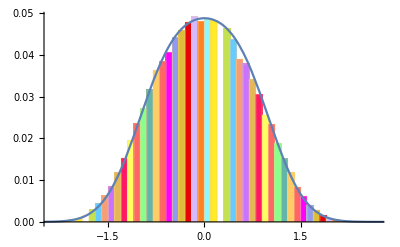

```mathematica
Show[%3,Plot[exp[Pi^2]/25,{t,-6,6}]]
```

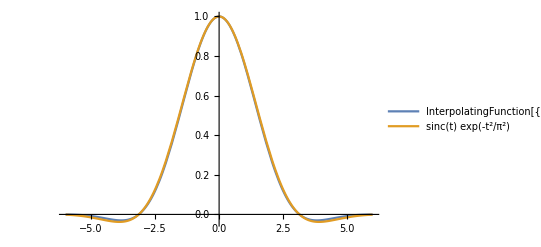

```mathematica
Plot[{Evaluate@Interpolation[raw,t],Sinc[t]Exp[-t^2/Pi^2]},{t,-6.,6.},PlotLegends->"Expressions"]
```

```mathematica
NonlinearModelFit[raw,Sinc[t]Exp[-t^2/a],{a},t]
```

FittedModel[ⅇ^(-0.110495 t^2) Sinc[t]]

```mathematica
%16["BestFitParameters"]
```

{a→9.05018}

```mathematica
exp[Pi^2]/25//FullSimplify
```

1/50 √(π/2) (-Erf[1/2 π (-1+t)]+Erf[1/2 π (1+t)])

```mathematica
Integrate[(1/50)*Sqrt[Pi/2]*(-Erf[(1/2)*Pi*(-1 + t)] + Erf[(1/2)*Pi*(1 + t)]),{ t,-Infinity,Infinity}]
```

(√(2 π))/25

```mathematica
exp[Pi^2]
```

1/2 √(π/2) (-Erf[1/2 π (-1+t)]+Erf[1/2 π (1+t)])